```mathematica
Quit
```

## Load paclet

```mathematica
PacletDirectoryLoad[ParentDirectory@NotebookDirectory[]];
```

```mathematica
PacletObject["ChristopherWolfram/GDALLink"]
```

PacletObject[…]

```mathematica
Needs["ChristopherWolfram`GDALLink`"]
```

## Experiments

```mathematica
$HistoryLength=0;
```

```mathematica
GDALInitialize[]
```

```mathematica
GDALDatasetImport["path/to/nowhere.shp"]
```

$Failed

### Example 1

```mathematica
dataset=GDALDatasetImport["/Users/christopher/Library/CloudStorage/Dropbox/mathematica/languageMaps/rawData/gmi_geodata/lang/langa.shp"]
```

GDALDataset[ManagedObject[…]]

```mathematica
dataset["LayerAssociation"]
```

<|langa→GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]]|>

```mathematica
dataset["LayerCount"]
```

1

```mathematica
layer=dataset["Layer",1]
```

GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]]

```mathematica
layer["FieldName"]//Length
```

16

```mathematica
data=layer["FieldTabular"];//EchoTiming
```

3.14603

```mathematica
data
```

```mathematica
Counts[Length/@data]
```

<|7612→16|>

```mathematica
data=layer["FieldAssociation"];//EchoTiming
```

2.11611

```mathematica
layer["RawFieldType",11]
```

12

```mathematica
Table[layer["RawFieldType",i],{i,0,100}]
```

{$Failed,4,4,4,4,4,4,4,4,4,4,4,12,4,4,4,4,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
layer["Name"]
```

langa

```mathematica
dataset["Layer","langa"]===layer
```

True

```mathematica
layer["ResetReading"]
```

```mathematica
layer["NextFeature"]
```

GDALFeature[GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]],ManagedObject[…]]

```mathematica
layer["RawLayerDefinition"]
```

OpaqueRawPointer[…]

```mathematica
layer["FieldCount"]
```

16

```mathematica
layer["RawFieldDefinition",0]
```

OpaqueRawPointer[…]

```mathematica
layer["RawFieldType",0]
```

4

```mathematica
layer["RawFieldType",-10]
```

$Failed

```mathematica
feature=layer["NextFeature"]
```

GDALFeature[GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]],ManagedObject[…]]

```mathematica
VectorLessEqual[{a,b,c}]
```

a\[VectorLessEqual]b\[VectorLessEqual]c

```mathematica
feature["Field",1]
```

PAE-ABW

```mathematica
feature["FieldList"]
```

{PAE-ABW,pap-ABW,pap-aw,pap-AA,Papiamentu,Papiamentu,PAPIAMENTU,Papiamentu,Americas,Aruba,60,000 in Aruba (1999),60000,Creole, Iberian based,L,Creole,CREOLE}

```mathematica
feature["FieldAssociation"]
```

<|ID→PAE-ABW,ID_ISO_A3→pap-ABW,ID_ISO_A2→pap-aw,ID_FIPS→pap-AA,NAM_LABEL→Papiamentu,NAME_PROP→Papiamentu,NAME2→PAPIAMENTU,NAM_ANSI→Papiamentu,CNT→Americas,C1→Aruba,POP→60,000 in Aruba (1999),LMP_POP1→60000,G→Creole, Iberian based,LMP_CLASS→L,FAMILYPROP→Creole,FAMILY→CREOLE|>

```mathematica
layer["ResetReading"];
feature=layer["NextFeature"];
```

```mathematica
feature=layer["NextFeature"];
```

```mathematica
Table[feature["FieldString",n],{n,layer["FieldCount"]}]
```

{PAE-ABW,pap-ABW,pap-aw,pap-AA,Papiamentu,Papiamentu,PAPIAMENTU,Papiamentu,Americas,Aruba,60,000 in Aruba (1999),60000,Creole, Iberian based,L,Creole,CREOLE}

```mathematica
feature["FieldString",0]
```

```mathematica
RepeatedTiming[GeoPolygon@@(FromGEOS@FromWKT@feature["GeometryWKT"]/.{a_?NumberQ,b_?NumberQ}:>{b,a});]
```

{0.00146871,Null}

```mathematica
GeoArea[GeoPolygon@@(FromGEOS@FromWKT@feature["GeometryWKT"]/.{a_?NumberQ,b_?NumberQ}:>{b,a})]
```

74577.3 mi^2

```mathematica
GeoGraphics[GeoPolygon@@(FromGEOS@FromWKT@feature["GeometryWKT"]/.{a_?NumberQ,b_?NumberQ}:>{b,a})]
```

-Graphics-

```mathematica
GeoGraphics@FromGEOS@FromWKT@feature["GeometryWKT"]
```

-Graphics-

```mathematica
data=ToTabular[layer["FeatureMap",#["FieldAssociation"]&]];//EchoTiming
```

7.96562

```mathematica
data
```

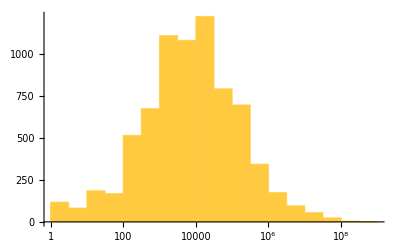

```mathematica
Histogram[Normal@data[[All,"LMP_POP1"]],{"Log",25}]
```

```mathematica
polygons=layer["FeatureMap",FromGEOS@FromWKT@#["GeometryWKT"]&];//EchoTiming
```

2.54367

```mathematica
geopolygons=layer["FeatureMap",GeoPolygon@@(FromGEOS@FromWKT@#["GeometryWKT"]/.{a_?NumberQ,b_?NumberQ}:>{b,a})&];//EchoTiming
```

3.15888

```mathematica
Rasterize@Graphics[{FaceForm[],EdgeForm[Thin],polygons},ImageSize->Large]
```

-Graphics-

### Example 2

```mathematica
dataset=GDALDatasetImport["/Users/christopher/Library/CloudStorage/Dropbox/UChicago/projects/districtingDynamics/rawData/ma_2020_gen_2020_blocks/ma_2020_gen_2020_blocks.shp"]
```

GDALDataset[ManagedObject[…]]

```mathematica
dataset=GDALDatasetImport["/Users/christopher/Downloads/tl_2024_25_tabblock20/tl_2024_25_tabblock20.shp"]
```

GDALDataset[ManagedObject[…]]

```mathematica
rawSHP=Import["/Users/christopher/Downloads/tl_2024_25_tabblock20/tl_2024_25_tabblock20.shp","Data"];//EchoTiming
```

11.764

```mathematica
Length@rawSHP[[1,4,2,1,2]]
```

107278

```mathematica
ToTabular[Association@rawSHP[[1,4,2]],"Columns"]
```

```mathematica
layer=dataset["Layer",1]
```

GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]]

```mathematica
ToTabular[layer["FeatureMap",#["FieldList"]&]];//EchoTiming
```

58.5083

```mathematica
data=ToTabular[layer["FeatureMap",#["FieldAssociation"]&]];//EchoTiming
```

108.28

```mathematica
Length@data
```

107278

```mathematica
data
```

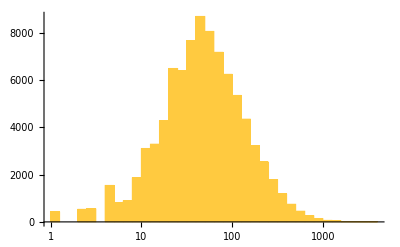

```mathematica
Histogram[Normal@data[[All,"POP20"]],{"Log",40}]
```

```mathematica
layer["Name"]
```

ma_2020_gen_2020_blocks

```mathematica
dataset["Layer","ma_2020_gen_2020_blocks"]===layer
```

True

```mathematica
layer["ResetReading"]
```

```mathematica
layer["NextFeature"]
```

GDALFeature[GDALLayer[GDALDataset[ManagedObject[…]],OpaqueRawPointer[…]],ManagedObject[…]]

```mathematica
(*Module[{n=0},layer["FeatureScan",n++&];n]//EchoTiming*)
```

```mathematica
layer["RawLayerDefinition"]
```

OpaqueRawPointer[…]

```mathematica
layer["FieldCount"]
```

14

```mathematica
layer["RawFieldDefinition",0]
```

OpaqueRawPointer[…]

```mathematica
layer["RawFieldType",0]
```

4

```mathematica
layer["RawFieldType",-10]
```

$Failed

```mathematica
layer["ResetReading"];
feature=layer["NextFeature"];
```

```mathematica
Table[feature["FieldString",n],{n,layer["FieldCount"]}]
```

{250010101001000,25,001,Provincetown Town Precinct 1,0,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000,0.000000000000000}

```mathematica
feature["FieldString",100]
```

```mathematica
polygons=layer["FeatureMap",FromGEOS@FromWKT@#["GeometryWKT"]&];//EchoTiming
```

13.5758

```mathematica
Length@polygons
```

107278

```mathematica
Rasterize@Graphics[{FaceForm[],EdgeForm[Thin],polygons},ImageSize->Large]
```

-Graphics-

## Scratch space

```mathematica
$GDALPath="/opt/homebrew/Cellar/gdal/3.8.5_2/lib/libgdal.dylib";
```

```mathematica
cGDALAllRegister=ForeignFunctionLoad[$GDALPath,"GDALAllRegister",{}->"Void"]
```

ForeignFunction[…]

```mathematica
RawMemoryExport["test"]
```

ManagedObject[…]

```mathematica
cGDALOpenEx=ForeignFunctionLoad[$GDALPath,"GDALOpenEx",{
"RawPointer"::["UnsignedInteger8"],
"CUnsignedInt",
"RawPointer"::["UnsignedInteger8"],
"RawPointer"::["UnsignedInteger8"],
"RawPointer"::["UnsignedInteger8"]
}->tGDALDatasetH]
```

ForeignFunction[…]

```mathematica
cGDALClose=ForeignFunctionLoad[$GDALPath,"GDALClose",{tGDALDatasetH}->"CInt"]
```

ForeignFunction[…]

```mathematica
tGDALDatasetH="OpaqueRawPointer";
```

```mathematica
$GDALConstants=<|
"GDAL_OF_VECTOR"->4
|>;
```

GDALDatasetH GDALOpenEx(
	const char *pszFilename,
	unsigned int nOpenFlags,
	const char *const *papszAllowedDrivers,
	const char *const *papszOpenOptions,
	const char *const *papszSiblingFiles
)

```mathematica
cGDALAllRegister[]
```

```mathematica
dataset=cGDALOpenEx["/Users/christopher/Library/CloudStorage/Dropbox/UChicago/projects/districtingDynamics/rawData/ma_2020_gen_2020_blocks/ma_2020_gen_2020_blocks.shp",$GDALConstants["GDAL_OF_VECTOR"],OpaqueRawPointer[0],OpaqueRawPointer[0],OpaqueRawPointer[0]]
```

OpaqueRawPointer[…]